# Integration of generic coupled-scalar-GB-eqs with radial perturbation

This notebook is aimed to study the stability of BH solutions in scalar-GB theory under radial perturbations.

```mathematica
Quit[];
```

### Needed files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Loading the system of equations from auxiliary file*)
perturbEQS=Import["Data/general_perturb_GBeqs.m"]; (*file containing the perturbed equation obtained by the notebook used in article 1903.06784_Gualtieri*)
backEQS=Import["Data/general_background_eqs.m"];(*file containing the background equations obtained by the notebook used in article 1903.06784_Gualtieri*)
perturbedG=Import["Data/perturbed_eqs_Georios.m"];(*file containing the perturbed equation used by Georgios*)
perturbedSCH=Import["Data/Schwarz_perturb_GBeqs.m"];
```

```mathematica
(*Load packages for numerical integration*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
(*Loading the fundamental branch inputs of η and ϕh: tab07 is the one computed by Gualtieri, b0 is Georgios' one and FundBranch is mine, which is the same as Gualtieri's but more detailed in the spacing of the η*)
```

```mathematica
TAB1=ReadList["Data/tab1.m"][[1]];
tabel={};
tab07={};
Do[If[TAB1[[i,2]]>0,Massa=(1/ TAB1[[i,3]]);tabel=AppendTo[tabel,{TAB1[[i,1]]*Massa^2,TAB1[[i,2]],Massa,TAB1[[i,4]]*Massa}]],{i,1,6000}];
Do[If[tabel[[i,1]]<=0.725,(*Print["η=", tabel[[i,1]] ," ","Massa=" ,tabel[[i,3]], " ","Q=", tabel[[i,4]]];*)tab07=AppendTo[tab07,tabel[[i]]]],{i,1,Length[tabel]}]

b0=Import["/home/dario/Documents/UNI/Tesi/Wolfram Mathematica/Stability/stability-Georgios/data/beta0zeta0.dat"];
b0new=Table[{b0[[i,1]]*4,b0[[i,2]],b0[[i,3]],b0[[i,4]]},{i,1,Length[b0]}];

FundBranch=ReadList["Data/toCheckStability_FundBranch.m"][[1]];
```

## Background fields integration

In this case we write the metric ds2 = −A(r)dt^2+ (B(r))^-1 dr^2 + r^2 dΩ^2. 
Now we simplify the background diff equations imposing α=1/2 and that we want a simple theory with no scalar field potential

```mathematica
BEQS=Simplify[backEQS//.{Vf->(0&),α->1/2}];
```

```mathematica
(*Define the coupling function we will study.*)
```

```mathematica
(*ruleCoupling={F-> ((η/8#^2+λ/16#^4)&)};*)
ruleCoupling={F-> ((η/8#^2)&)};
```

```mathematica
Rh=1;(*Setting the event horizon value*)
```

### Background Boundary conditions

```mathematica
Clear[A,B,ϕ]
```

I expand metric functions and the scalar field around Rh, the event horizon, which is set to 1 without loss of generality

```mathematica
(*A[r_]:=Sum[Subscript[ai, i](r-1)^i,{i,1,5}];
B[r_]:=Sum[Subscript[bi, i](r-1)^i,{i,1,5}];
ϕ[r_]:=Sum[Subscript[fi, i](r-1)^i,{i,0,5}];*)
```

Now the expansion around horizon of the background equations

```mathematica
(*eqshor=Series[{BEQS[[1]],BEQS[[2]],BEQS[[3]](r-1)},{r,1,4}];*)
```

Coefficients of the terms of first and second order in (r-1) powers of the bck equations

```mathematica
(*eqshor1=Table[SeriesCoefficient[eqshor[[i]],0],{i,1,3}];
eqshor2=Table[SeriesCoefficient[eqshor[[i]],1],{i,1,3}];*)
```

```mathematica
(*eqshor1[[3]]//Simplify*)
```

Obtaining analytical solutions for some of the coefficients of the metric functions and the field

```mathematica
(*shor1=Solve[eqshor1==0,{Subscript[fi, 1],Subscript[bi, 1]}][[2]];
shor2=Solve[eqshor2==0,{Subscript[fi, 2],Subscript[bi, 2],Subscript[ai, 2]}][[1]];*)
```

This is the coefficient of the derivative of the field and the expression under sqrt is the one I use to find phimax in scalarization integration

```mathematica
(*shor1[[1]]//Simplify*)
```

Joining the rules for the background

```mathematica
(*shorf=Join[shor1,shor2];*)
```

```mathematica
(*shorf>>"Data/expanded_bck_BCS_hor.m"*)
```

```mathematica
BCSbckHor=<<"Data/expanded_bck_BCS_hor.m";
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};
```

### Background Integration

I’ll work with compactified coordinate x=1-rh/r so that the event horizon is mapped at x->0 and r->∞ is at x->1

```mathematica
(*CBEQ are the background equations in compactified coordinates*)
```

```mathematica
CBEQ=(1-x)^3 BEQS/.{A->(A[1-Rh/#]&),B->(B[1-Rh/#]&),ϕ->(ϕ[1-Rh/#]&)}/.r->Rh/(1-x)//Simplify;
```

```mathematica
Clear[CsGBINT];
```

CsGBINT:   (rh, ϕh, η, λ, rmax, Nh, ruleCoupling, ) ->  (ϕinf, ϕ[r],ϕ'[r],A[r],A'[r],B[r],B'[r],ϕ0,Q/M, η/M^2,λ/M^2,M )   Integration of the equations for a given choice of rh, ϕh, η, λ

```mathematica
CsGBINT[rh0_,phic0_,η0_,λ0_,xmax0_,xinf_,MODEL_,ϵ0_]:=(
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*ϵ0 difines how far from the horizon we will start our integrations*)

(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.{η->η0,λ->λ0}/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOU=Thread[{A[x],B[x],ϕ[x],(-1+x)^2 ϕ'[x]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0/.r->1/(1-x))]/.x->ϵ0;
(*(*mi fermo al primo ordine in espansione intorno all'orizzonte*)
BCS={
A[r]==N[r-rh],
B[r]==N[r-rh],
ϕ'[r]==N[(rh0/(4 F'[ϕ[r]]))(-1+Sqrt[1-96 ((F'[ϕ[r]])^2/rh^4)])](*/.r->rh0/(1-x)*)//.Union[MODEL,{η->η0, λ->λ0}],
(*condizione necessaria affinché ϕ'' non diverga all'orizzonte.*)
ϕ[r]==phic0
}/.{A->(A[1-rh0/#]&),B->(B[1-rh0/#]&),ϕ->(ϕ[1-rh0/#]&)}//.r->rh0/(1-x)//.{x->ϵ0,η-> η0, λ->λ0,rh->rh0};*)
BCS=BOU;
(*Numerical integration*)
sol=NDSolve[
Union[Union[{CBEQ[[2]]==0,CBEQ[[1]]==0, CBEQ[[3]]==0}//.Union[MODEL,{η->η0, λ->λ0}]],BCS],
{A,B,ϕ},
{x,ϵ0,xmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsol=ϕ[x]/.sol;
Dϕsol=D[ϕsol,x];
Asol=A[x]/.sol;
DAsol=D[Asol,x];
Bsol=B[x]/.sol;
DBsol=D[Bsol,x];
(*Values of variables at infinity*)
ϕinf=ϕsol/.{x-> xmax0};
Ainf=Asol/.{x-> xmax0};
Binf=Bsol/.{x-> xmax0};
Asolshift=Asol/Ainf;


PhysicalParams=NSolve[{
Asolshift==1-(2 M)/r+((M Q^2)/(12 r^3)),
ϕsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
((1-x)^2/rh0)D[ϕsol,x]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 }/.r->rh0/(1-x)/.{x->xinf},{ϕ0,Q,M}][[1]];
(*Output: ϕinf, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)
{ϕinf,
ϕsol,
Dϕsol,
Asol*(Binf/Ainf),
DAsol*(Binf/Ainf),
Bsol(*/Binf*),
DBsol(*/Binf*),
ϕ0/.PhysicalParams,
(Q/M)/.PhysicalParams,
(η0/M^2)/.PhysicalParams,
(λ0/M^2)/.PhysicalParams,
M/.PhysicalParams
}
);
```

I also report the integration in radial coordinate which is useful then for the effective potential study and to have the constant Wronskian for the perturbed eq. solutions

```mathematica
sGBINT[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_,ϵ0_]:=(
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.{η->η0,λ->λ0}/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOUr=Thread[{A[r],B[r],ϕ[r],ϕ'[r]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0)]/.r->rh0+ϵ0;

BCSr={
A[r]==N[r-rh],
B[r]==N[r-rh],
ϕ'[r]==N[(rh/(4 F'[ϕ[r]]))(-1+Sqrt[1-96 ((F'[ϕ[r]])^2/rh^4)])]//.Union[MODEL,{η->η0, λ->λ0}],
(*condizione necessaria affinché ϕ'' non diverga all'orizzonte.*)
ϕ[r]==phic0
}//.{r->rh0+ϵ0,rh-> rh0,η-> η0, λ->λ0,ϕ[rh]->phic0};

BCSr=BOUr;
(*Numerical integration*)
solr=NDSolve[
Union[Union[{BEQS[[2]]==0,BEQS[[1]]==0, BEQS[[3]]==0}//.Union[MODEL,{η->η0, λ->λ0}]],BCSr],
{A,B,ϕ},
{r,rh0+ϵ0,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsolr=ϕ[r]/.solr;
Dϕsolr=D[ϕsolr,r];
Asolr=A[r]/.solr;
DAsolr=D[Asolr,r];
Bsolr=B[r]/.solr;
DBsolr=D[Bsolr,r];
(*Values of variables at infinity*)
ϕinfr=ϕsolr/.{r-> rmax0};
Ainfr=Asolr/.{r-> rmax0};
Binfr=Bsolr/.{r-> rmax0};
Asolshiftr=Asolr/Ainfr;

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Asolshiftr==1-(2 Mr)/r+((Mr *Qr^2)/(12 r^3)),
ϕsolr==ϕ0r+Qr/r+(Mr* Qr)/r^2+((32 Mr^2 Qr-Qr^3)/(24 r^3)),
D[ϕsolr,r]==D[ϕ0r+Qr/r+(Mr* Qr)/r^2,r]&&Mr≥ 0 }/.{r->rh0*NHorizons0},{ϕ0r,Qr,Mr}][[1]];

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Nell'output restituisco l'esponenziale delle funzioni metriche Υ e Λ, che chiamo A[r] e B[r]*)

(*Output: ϕ0, ϕinf, Q/M, η/M^2, λ/M^2, M, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)
{ϕ0r/.PhysicalParams,
ϕinfr,
(Qr/Mr)/.PhysicalParams,
(η0/Mr^2)/.PhysicalParams,
(λ0/Mr^2)/.PhysicalParams,
Mr/.PhysicalParams,
ϕsolr,
Dϕsolr,
Asolr/Ainfr,
DAsolr/Ainfr,
Bsolr(*/Binf*),
DBsolr(*/Binf*)
}
);
```

## Perturbed integration

### Perturbed equations

I’m interested in the simplest case where the potential Vf = 0. Moreover the perturbEQS has a constant value α which can be set to 1/2 for the whole analysis: in fact it varies depending on the metric used for the background field integration, i.e.  if the metric functions are defined as exp(Υ) or exp(2Υ), etc.

The equation we need is the following: - ∂^2 φ1/∂r^2  + h(r) ∂^2 φ1/∂t^2 + k(r)∂φ1/∂r +p(r)φ1=0. In perturbEQS we have this equation but in a more general form, so we have to simplify it a little for our problem.

```mathematica
(*Georgios' equations*)
```

```mathematica
PEQG=perturbedG//.α->η/4;
```

```mathematica
PEQGx=PEQG/(1-x)^4/.{A->(A[1-1/#]&),B->(B[1-1/#]&),ϕ->(ϕ[1-1/#]&),ϕ1->(ϕ1[1-1/#]&)}/.r->Rh/(1-x)//Simplify;
```

```mathematica
PEQGsch=PEQGx/.{ϕ->(0&),A->(#&),B->(#&)}//Simplify
```

((x^4 (1-60 η)+x^2 (3-18 η)+45 x^5 η-18 x^6 η+3 x^7 η+x (-1+3 η)+x^3 (-3+45 η)+ω^2) ϕ1[x]+(-1+x)^3 x ((-1+3 x) ϕ1'[x]+(-1+x) x ϕ1''[x]))/((-1+x)^4 x^2)

```mathematica
(*Salcedo's equations*)
```

```mathematica
PEQS=Simplify[perturbEQS//.{Vf[ϕ[r]]->0, Vf'[ϕ[r]]->0,Vf''[ϕ[r]]->0,α->1/2}];
```

```mathematica
PEQSom=PEQS/.ϕ1->(φ[#2]Exp[-I ω #1]&)/.t->0//Simplify;
```

```mathematica
CPEQS=PEQSom/.{A->(A[1-1/#]&),B->(B[1-1/#]&),ϕ->(ϕ[1-1/#]&),φ->(φ[1-1/#]&)}/.r->Rh/(1-x)//Simplify;
(*toNorm=Coefficient[CPEQS,φ''[x]];
CPEQS2=CPEQS/toNorm//Simplify;*)
```

```mathematica
(*for the Schwarzschild background*)
```

```mathematica
CPEQsch=perturbedSCH/.Vf->(0&)/.α->1/2/.ϕ1->((φ[#2]Exp[-I ω #1])&)/.t->0/.φ->(φ[1-1/#]&)/.r->1/(1-x)//Simplify
```

1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
CPEQsch
```

1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

### Boundary conditions near horizon

```mathematica
(*Clear[A,B,ϕ,φ]*)
```

```mathematica
(*numero=1;
xm=0.5;
tab=FundBranch;
eta=tab[[numero,1]];
phic0=tab[[numero,2]];
out2=PINTEGx[Rh,phic0,eta,0,10^12,150,ruleCoupling,0.09,xm,10^-8];
phiminG=out2[[1]];
phipluG=out2[[3]];
DphiminG=out2[[2]];
DphipluG=out2[[4]];*)
```

```mathematica
(*bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->Rh^-1/.rh->Rh/.r->1/(1-x)*)
```

```mathematica
(*ruleHorizon=Solve[Thread[{A[x],B[x],ϕ[x],(-1+x)^2 ϕ'[x]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->Rh^-1/.rh->Rh/.r->1/(1-x))],{A[x],B[x],ϕ[x],ϕ'[x]}]*)
```

```mathematica
(*Ahor'[x]=D[A[x]/.ruleHorizon,x][[1]]//Simplify;
Bhor'[x]=D[B[x]/.ruleHorizon,x][[1]]//Simplify;*)
```

```mathematica
(*ruleHorFull=Join[ruleHorizon[[1]],{A'[x]->Ahor'[x],B'[x]->Bhor'[x]}]*)
```

```mathematica
(*φ[x_]:=Sum[Subscript[ph, i](x)^i,{i,0,3}]*)
```

```mathematica
(*φ[x]*)
```

```mathematica
(*cpeqexphor=CPEQS/.ruleCoupling/.ruleHorFull/.{η->eta,ω^2->-0.09^2}//Simplify;*)
```

```mathematica
(*cpeqexphor0=SeriesCoefficient[cpeqexphor,{x,0,0}];
cpeqexphor1=SeriesCoefficient[cpeqexphor,{x,0,1}];*)
```

```mathematica
(*bcshor0=(Solve[cpeqexphor0==0(*/.Subscript[ph, 0]->N[Exp[0.09 *tortSch[x]]]*),{Subscript[ph, 1]}]/.x->10^-8//Simplify)[[1]]
bcshor1=(Solve[cpeqexphor1==0/.Subscript[ph, 0]->N[Exp[0.09 *tortSch[x]]]/.bcshor0,{Subscript[ph, 2]}]/.x->10^-8//Simplify)[[1]]*)
```

```mathematica
(*PBCSmin*)
```

```mathematica
(*3.7857682062432075*^15 *0.2084906119958683*)
```

### Integration functions

#### Schwarzschild BH background

INPUT:  rh,  ϕh,  η,  λ,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
GPINTEGsch[rh0_,η0_,λ0_,ω0_,xm_ ,ϵ0_]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.
Remember that First derivative must be constant at the boundary, not strictly zero*)

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
ϕ1[x]==N[Exp[ω0 *tortSch[x]]],
ϕ1'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

PBCSminusSCH={
ϕ1[x]==0,
ϕ1'[x]==cons 
}//.{x->xmin, cons->cminus};
(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
ϕ1[x]==0(*φSCH//.x->xmax*),
ϕ1'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{PEQGsch==0//.{ω^2->- ω0^2,rh->rh0,η->η0,λ->λ0}},PBCSminSCH],ϕ1,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{PEQGsch==0//.{ω^2->- ω0^2,rh->rh0,η->η0,λ->λ0}},PBCSplusSCH],ϕ1,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=ϕ1[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=ϕ1[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

INPUT:  rh,  ϕh,  η,  λ,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
PINTEGsch[rh0_,η0_,λ0_,MODEL_,ω0_,xm_ ,ϵ0_]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.
Remember that First derivative must be constant at the boundary, not strictly zero*)

CPEQschw=CPEQsch/.MODEL;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
φ[x]==0(*φSCH//.x->xmax*),
φ'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0,η->η0,λ->λ0}},PBCSminSCH],φ,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0,η->η0,λ->λ0}},PBCSplusSCH],φ,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=φ[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=φ[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

#### Scalarized BH solutions

The first function here is the one which uses Georgios’ perturbed equation so there every object name has a G as suffix or prefix referring to him. The second one uses my pert eq. 
They both have the same inputs and outputs

INPUT:  rh,  ϕh,  η,  λ,  rmax[r],  Nhorizons,  ruleCoupling,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

note:  rh is always set to 1; rmax is given in r and it’s used for the CsGBINT, same as Nhorizons;  ωi is the Imaginary part of the frequency (Real number)

```mathematica
GPINTEG[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_ ,ϵ0_]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->11,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xmax=0.99;
xinf=0.9999;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: rh,ϕh,η,λ,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, η/M^2, λ/M^2, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

BCKGRND=CsGBINT[rh0,phic0,η0,λ0,1-1/rmax0,1-1/NHorizons0,MODEL,ϵ0];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFFG={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};
(*ruleCOEFFG={A->((AA[#])&), B->((BB[#])&), ϕ->((ϕbck[#])&)};*)
ruleCOEFFsch={A->(#&), B->(#&),  ϕ->(0&)};


(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
(*NOTE: If you want to compute the CPEQ with the normalized solutions instead of /.sol you need to pass /.ruleCOEFFG*)  
CPEQG=PEQGx/.{η->η0,λ->λ0,rh->rh0}/.ruleCOEFFG;

(*Perturbed equation for the Schwarzschild solution*)
CPEQsch=PEQGx/.{η->η0,λ->λ0,rh->rh0}/.ruleCOEFFsch;


(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSmin={
ϕ1[x]==N[Exp[ω0 *tortSch[x]]],
ϕ1'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.
Remember that First derivative must be constant at the boundary, not strictly zero*)
PBCSminus={
ϕ1[x]==0,
ϕ1'[x]==cons 
}//.{x->xmin, cons->cminus};

(*(*====*)
(*In order to give the correct boundary cond. for the integration towards horizon, let's first integrate as for Schwarzschild Background*)
PBCSplussch={
ϕ1[x]==0,
ϕ1'[x]==cons
}//.{x->xinf, cons->cplus};
(*integration*)
SOLsch=NDSolve[Union[{CPEQsch==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplussch],ϕ1,
{x,xinf,xmax},
rulePAR];
φSCH=ϕ1[x]/.SOLsch;
DφSCH=D[φSCH,x];
(*====*)*)

(*Boundary conditions for the integration towards infinity*)
PBCSplus={
ϕ1[x]==0(*φSCH//.x->xmax*),
ϕ1'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQG==0//.{ω^2->- ω0^2,rh->rh0}},PBCSmin(*us*)],ϕ1,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQG==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],ϕ1,
{x,xmax,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=ϕ1[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=ϕ1[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
PINTEGx[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_,ϵ0_ ]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,PrecisionGoal->11,AccuracyGoal->11,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

ϵ2=10^-15;(*How far from the horizon we will start our integrations*)
xmin=ϵ0;
xmax=0.99;
xinf=0.999;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: rh,ϕh,η,λ,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, η/M^2, λ/M^2, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

BCKGRNDr=sGBINT[rh0,phic0,η0,λ0,rmax0,NHorizons0,MODEL,ϵ2];
BCKGRND=CsGBINT[rh0,phic0,η0,λ0,1-1/rmax0,1-1/NHorizons0,MODEL,ϵ0];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFF={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};

(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
CPEQ=CPEQS/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.(*sol*)ruleCOEFF;

PEQ=PEQSom/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.solr;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSmin={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};


(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.
Remember that First derivative must be constant at the boundary, not strictly zero*)
PBCSminus={
φ[x]==0,
φ'[x]==cons 
}//.{x->xmin, cons->cminus};

(*(*====*)
(*In order to give the correct boundary cond. for the integration towards horizon, let's first integrate as for Schwarzschild Background*)
PBCSplussch={
φsch[x]==0,
φsch'[x]==cons
}//.{x->xinf, cons->cplus};
(*integration*)
SOLsch=NDSolve[Union[{CPEQsch[x]==0//.{ω->I ω0,rh->rh0}},PBCSplussch],φsch,
{x,xinf,xmax},
rulePAR];
φSCH=φsch[x]/.SOLsch;
DφSCH=D[φSCH,x];
(*====*)*)

(*Boundary conditions for the integration towards infinity*)
PBCSplus={
φ[x]==0(*/.x->xmax*),
φ'[x]==cons(*/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSmin(*us*)],φ,
{x,xmin,xm(*+0.3*)+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],φ,
{x,xmax,xm(*-0.3*)-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=φ[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=φ[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
PINTEGxbou[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_,ϵ0_ ]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,PrecisionGoal->11,AccuracyGoal->11,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

ϵ2=10^-15;(*How far from the horizon we will start our integrations*)
xmin=ϵ0;
xmax=0.99;
xinf=0.999;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: rh,ϕh,η,λ,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, η/M^2, λ/M^2, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

BCKGRNDr=sGBINT[rh0,phic0,η0,λ0,rmax0,NHorizons0,MODEL,ϵ2];
BCKGRND=CsGBINT[rh0,phic0,η0,λ0,1-1/rmax0,1-1/NHorizons0,MODEL,ϵ0];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFF={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};

ruleHorizon=Solve[Thread[{A[x],B[x],ϕ[x],(-1+x)^2 ϕ'[x]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0^-1/.rh->rh0/.r->rh0/(1-x))],{A[x],B[x],ϕ[x],ϕ'[x]}];
Ahor'[x]=D[A[x]/.ruleHorizon,x][[1]]//Simplify;
Bhor'[x]=D[B[x]/.ruleHorizon,x][[1]]//Simplify;

ruleHorFull=Join[ruleHorizon[[1]],{A'[x]->Ahor'[x],B'[x]->Bhor'[x]}];
φ[x_]:=Sum[Subscript[ph, i](x)^i,{i,0,3}];

cpeqexphor=CPEQS/.MODEL/.ruleHorFull/.{η->eta,ω^2->-ω0^2}//Simplify;
cpeqexphor0=SeriesCoefficient[cpeqexphor,{x,0,0}];
cpeqexphor1=SeriesCoefficient[cpeqexphor,{x,0,1}];

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];
bcshor0=(Solve[cpeqexphor0==0/.Subscript[ph, 0]->N[Exp[ω0*tortSch[x]]],{Subscript[ph, 1]}]/.x->xmin//Simplify)[[1]];
bcshor1=(Solve[cpeqexphor1==0/.Subscript[ph, 0]->N[Exp[ω0 *tortSch[x]]]/.bcshor0,{Subscript[ph, 2]}]/.x->xmin//Simplify)[[1]];

Clear[φ];

(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
CPEQ=CPEQS/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.(*sol*)ruleCOEFF;


PEQ=PEQSom/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.solr;


(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.
Remember that First derivative must be constant at the boundary, not strictly zero*)
PBCSm={
φ[x]==N[Exp[ω0*tortSch[x]]],
φ'[x]==Subscript[ph, 1]/.bcshor0
}//.{x->xmin};


(*Boundary conditions for the integration towards infinity*)
PBCSplus={
φ[x]==0(*/.x->xmax*),
φ'[x]==cons(*/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSm],φ,
{x,xmin,xm(*+0.3*)+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],φ,
{x,xmax,xm(*-0.3*)-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=φ[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=φ[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
PINTEGxUlti[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_,ϵ0_ ]:=(
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,PrecisionGoal->11,AccuracyGoal->11,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

ϵ2=10^-15;(*How far from the horizon we will start our integrations*)
xmin=ϵ0;
xmax=0.99;
xinf=0.999;

rmin=rh0/(1-xmin);
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: rh,ϕh,η,λ,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, η/M^2, λ/M^2, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

BCKGRNDr=sGBINT[rh0,phic0,η0,λ0,rmax0,NHorizons0,MODEL,ϵ2];
BCKGRND=CsGBINT[rh0,phic0,η0,λ0,1-1/rmax0,1-1/NHorizons0,MODEL,ϵ0];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFF={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};

(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
CPEQ=CPEQS/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.(*sol*)ruleCOEFF;
(*compactified perturbed equation divided by the coefficient of φ''[x] term*)

PEQ=PEQSom/.MODEL/.{η->η0,λ->λ0,rh->rh0}/.solr;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
coefome=Coefficient[PEQ,ω^2];
PEQ2=PEQ/.ω->0(*//Simplify*);
coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];

coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];(*-h: lui è -h perché derivando 2 volte rispetto al tempo porto giù un (-I)^2 e h era preso invece prima di derivare*)

(*Defining coefficients functions as in Doneva's paper*)
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;

tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)]; (*tortoise coordinate for Schwarzschild background*)

tortoise=NDSolve[{rstar'[rr]-g[rr]==0,rstar[rmin]==tortSch[xmin]},rstar,{rr,1+10^-9,100},rulePAR][[1]];
tortScal=rstar[rr]/.tortoise;
tortScalx=tortScal/.rr->rh0/(1-x);

PBCSmin={
φ[x]==N[Exp[ω0 *tortScalx]],
φ'[x]==N[D[Exp[ω0 *tortScalx],x]]}//.{x->xmin};


(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.*)

(*Boundary conditions for the integration towards infinity*)
PBCSplus={
φ[x]==0(*/.x->xmax*),
φ'[x]==cons(*/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSmin(*us*)],φ,
{x,xmin,xm(*+0.3*)+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],φ,
{x,xmax,xm(*-0.3*)-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=φ[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=φ[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
(*numero=1;
xm=0.5;
tab=FundBranch;
eta=tab[[numero,1]];
outG=GPINTEG[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,0.09,xm,2*10^-16];
outx=PINTEGx[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,0.09,xm,10^-8];
phiminG=outG[[1]];
phipluG=outG[[3]];
DphiminG=outG[[2]];
DphipluG=outG[[4]];
phiminDx=outx[[1]];
phipluDx=outx[[3]];
DphiminDx=outx[[2]];
DphipluDx=outx[[4]];*)
```

```mathematica
(*outxb=PINTEGxbou[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,0.09,xm,10^-10];
phiminDxb=outxb[[1]];
phipluDxb=outxb[[3]];
DphiminDxb=outxb[[2]];
DphipluDxb=outxb[[4]];*)
```

```mathematica
(*Plot[{Legended[phiminG,"G"],Legended[phiminDx,"x"],Legended[phiminDxb,"xb"]},{x,xmin,xm}]*)
```

### Tortoise coordinate and Effective potential

I want to compute the solution in the tortoise coordinate R defined as dR/dr=g, where g is the square root of the coefficient of the perturbed differential equation written in this way:
g^2 (∂^2 φ)/(∂t^2)-(∂^2 φ)/(∂r^2)+C (∂φ)/(∂r)+Uφ=0, so in our case (g^2) =-Hr/Nr. In this way I can write the differential equation in this form (-d^2/dR^2+ Veff)Z=ω^2Z and so that the Wronskian computed with respect to the tortoise coordinate is constant. Z is such that φ=F * Z and F satisfies the equation (2F')/F=C-g'/g with all this functions dependent on r

```mathematica
(*numero=1;
xm=0.5;
tab=FundBranch;
eta=tab[[numero,1]];
out=PINTEGx[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,minima[[numero,2]],xm,2*10^-9];
out2=GPINTEG[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,minima[[numero,2]],xm,2*10^-16];
phimin=out[[1]];
Dphimin=out[[2]];
phiplus=out[[3]];
Dphiplus=out[[4]];
phiminG=out2[[1]];
DphiminG=out2[[2]];
phiplusG=out2[[3]];
DphiplusG=out2[[4]];*)
```

```mathematica
(*minima[[numero,2]]*)
```

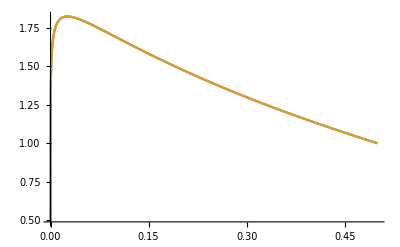

```mathematica
Plot[{pmin4,pmin5},{x,xmin,xm}]
```

```mathematica
(*GraphicsRow[{Plot[phimin,{x,2*10^-16,xm+0.3}],Plot[phiplus,{x,xm-0.3,0.99}]}]*)
```

```mathematica
(*coefome=Coefficient[PEQ,ω^2];
coefomeG=Coefficient[CPEQG,ω^2];*)
```

```mathematica
(*PEQ2=PEQ/.ω->0(*//Simplify*);
PEQG2=CPEQG/.ω->0;*)
```

```mathematica
(*PEQ2==PEQ-coefome*ω^2*)
```

```mathematica
(*coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];
coefG=Coefficient[PEQG2,{ϕ1[x],ϕ1'[x],ϕ1''[x]}];
coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];(*-h: lui è -h perché derivando 2 volte rispetto al tempo porto giù un (-I)^2 e h era preso invece prima di derivare*)
coefCG=coefG[[2]];(*k*)
coef1G=coefG[[3]];(*n*)
coefUG=coefG[[1]];(*p*)
coefgG=Coefficient[coefomeG,ϕ1[x]];(*-h: lui è -h perché derivando 2 volte rispetto al tempo porto giù un (-I)^2 e h era preso invece prima di derivare*)*)
```

```mathematica
(*GraphicsRow[{Plot[{-coef1/coef1,-coefC/coef1,-coefU/coef1,-coefg/coef1},{r,1,10}],Plot[{-coef1G,coefCG,coefUG,coefgG},{x,0.0001,0.99}]}]*)
```

```mathematica
(*(*Defining coefficients functions as in Doneva's paper*)
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;

gG[rr_]:=Sqrt[(coefgG/coef1G)]/.x->1-1/rr//Simplify;
cG[rr_]:=-coefCG/coef1G/.x->1-1/rr//Simplify;
uG[rr_]:=-coefUG/coef1G/.x->1-1/rr//Simplify;*)
```

```mathematica
(**)
```

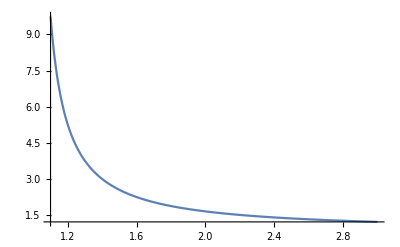

```mathematica
(*Plot[g[rr],{rr,1.1,3},PlotRange->Full]*)
```

```mathematica
(*g[40]*)
```

```mathematica
(*(*this is the differential equation that the function ff[r] (difined by φ[r]=ff[r]Z[r]) must satisfy*)
Clear[eqtortoise];
eqtortoise[rr_]:=(2fun'[rr]/fun[rr]-c[rr]+g'[rr]/g[rr]);
eqtortoiseG[rr_]:=(2fun'[rr]/fun[rr]-cG[rr]+gG'[rr]/gG[rr]);*)
```

```mathematica
(*(*integration*)
BCfun=fun[Rh+10^-6]==1;
SOLfun=NDSolve[{eqtortoise[rr]==0,BCfun},fun,{rr,1+10^-5,20},rulePAR][[1]];
ff[rr_]:=fun[rr]/.SOLfun;
BCfunG=fun[Rh+10^-6]==1;
SOLfunG=NDSolve[{eqtortoiseG[rr]==0,BCfunG},fun,{rr,1+10^-5,20},rulePAR][[1]];
ffG[rr_]:=fun[rr]/.SOLfunG;*)
```

```mathematica
(*Plot[{ff[rr],ffG[rr]},{rr,Rh+10^-2,3},PlotRange->Full]*)
```

```mathematica
(*DChange[x_]:=(1-x)^2/Rh;*)
```

```mathematica
(*(*Passing again to r coordinate for the solutions that are computed in the compactified coordinate x*)
phiminr[rr_]:=phimin/.x->{1-Rh/rr};
Dphiminr[rr_]:=DChange[x]^-1*Dphimin/.x->{1-Rh/rr};
phiplur[rr_]:=phiplus/.x->{1-Rh/rr};
Dphiplur[rr_]:=DChange[x]^-1*Dphiplus/.x->{1-Rh/rr};
phiminrG[rr_]:=phiminG/.x->{1-Rh/rr};
DphiminrG[rr_]:=DChange[x]^-1*DphiminG/.x->{1-Rh/rr};
phiplurG[rr_]:=phiplusG/.x->{1-Rh/rr};
DphiplurG[rr_]:=DChange[x]^-1*DphiplusG/.x->{1-Rh/rr};*)
```

```mathematica
(*GraphicsRow[{Plot[phiminr[rr],{rr,Rh/(1-2*10^-16),5},PlotRange->Full],Plot[phiplur[rr],{rr,2,Rh/(1-0.99)},PlotRange->Full]}]*)
```

```mathematica
(*
(*Computing the Z^(-) and Z^(+) functions according to φ[r]=ff[r]Z[r]*)
Zmin[rr_]:=phiminr[rr]/ff[rr];
Zplus[rr_]:=phiplur[rr]/ff[rr];
ZminG[rr_]:=phiminrG[rr]/ffG[rr];
ZplusG[rr_]:=phiplurG[rr]/ffG[rr];

(*Finally I can compute the Wronskian in tortoise coordinate, whose value doesn't depend on the matching point*)
WRO[rm_]:=g[rm]^-1(Zmin[rm]*Zplus'[rm]-Zplus[rm]*Zmin'[rm])(*/(ff[rm]^2 Zmin'[rm]*Zplus'[rm]+ff'[rm]*Zmin[rm]Zplus[rm])*);
WROGG[rm_]:=gG[rm]^-1(ZminG[rm]*ZplusG'[rm]-ZplusG[rm]*ZminG'[rm])*)
```

```mathematica
(*Table[WRO[i][[1]],{i,2,5}]*)
```

```mathematica
(*Table[WROGG[i][[1]],{i,2,5}]*)
```

```mathematica
(*Plot[{WRO[rm],WROGG[rm]},{rm,1.25,5},PlotRange->{-10^-16,10^-9}]*)
```

```mathematica
(*Veff[rr_]:=g[rr]^-2 (u[rr]-ff''[rr]/ff[rr]-c[rr]/ff[rr] ff'[rr]);
VeffG[rr_]:=gG[rr]^-2 (uG[rr]-ffG''[rr]/ffG[rr]-cG[rr]/ffG[rr] ffG'[rr]);
CVeff[x_]:=Veff[rr]/.rr->Rh/(1-x);*)
```

```mathematica
(*Veff[5]*)
```

```mathematica
(*Plot[{Veff[rr],VeffG[rr]},{rr,1.0001,3}, PlotRange->Full]*)
```

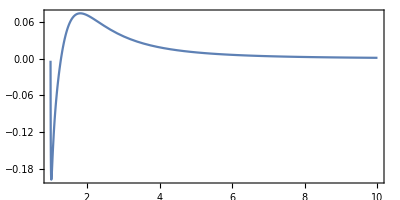
-Graphics-r/r_hV_effr_h^2

```mathematica
(*Labeled[GraphicsRow[{Plot[Veff[rr],{rr,1.0001,10}, PlotRange->Full,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]](*,Plot[CVeff[x],{x,0.1,0.9}, PlotRange->Full]*)}],{"r/r_h","V_effr_h^2"},{Bottom,Left}]*)
```

## Shooting method with Wronskian

Here we search for the eigenvalue ωi corresponding to the frequency at which the Wronskian W = [φ^(-)(dφ^(+)/dx)- (dφ^(-)/dx) φ^(+)]_(x=x_m) vanishes

### Schwarzschild BH

```mathematica
WRONSKsch[η0_,λ0_, ω0_, xm_,ϵ0_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGsch[1,η0,λ0,ruleCoupling,ω0,xm,ϵ0];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];

{Wrons1,
Wrons2,
prod}
);
```

Here in green there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value and for Sch. Background.
I checked the last value of η at which we have scalarized solution up to the forth decimal place is ηi=0.7256

```mathematica
(*
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=800;

lambda=10^-12;

wi=0.2;
wf=0.4;
step=(wf-wi)/pts;

ηi=1.8407125000000002;
ηf=2;
epts=25;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
etap[z_]:=ηi+(ηf-ηi)/epts(z-1);
(*tab=SchwBckSol;*)

xnear=2*10^-16;
minimaSch={};
Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WROGsch[k]={};
ηk=etap[k];(*tab[[k,1]];*)
Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSKsch[ηk,lambda,ωshoot,xmiddle,xnear](*[[1,1]]*);
WROGsch[k]=AppendTo[WROGsch[k],{ωshoot,check[[1]]}]},{j,1,pts}],j];
min=Min[Table[WROGsch[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROGsch[k]//Abs,min][[1,1]];
omegaok=WROGsch[k][[pos,1]];
minimaSch=AppendTo[minimaSch,{ηk,omegaok}]
,{k,1,epts}]
,k];*)
```

### Scalarized BH

```mathematica
WRONSK[phih0_,η0_,λ0_,MODEL_, ω0_, xm_,ϵ0_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=GPINTEG[Rh,phih0,η0,λ0,10^12,150,MODEL,ω0,xm,ϵ0];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
(*Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];
*)
{Wrons1(*,
Wrons2,
prod*)}
);
```

```mathematica
(*out3=PINTEGxbou[Rh,tab[[numero,2]],eta,0,10^12,150,ruleCoupling,0.11449999999999999,xm,10^-8]*)
```

```mathematica
(*PINTEGxUlti[Rh,tab[[1,2]],tab[[1,1]],lambda,10^12,150,ruleCoupling,0.01,xmiddle,xnear]*)
```

```mathematica
(*check2ew=WRONSK[tab[[1,2]],tab[[1,1]],0,ruleCoupling,-minima[[1,2]],0.5,10^-8]*)
```

{0.853152}

```mathematica
(*{-0.007071011619694367}*)
```

Here in orange there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value

```mathematica
(*xmmin=xmed[[Position[Wxmed,Min[Wxmed]][[1]]]]*)
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=100;

lambda=10^-12;

wi=0.01;
wf=0.15;
step=(wf-wi)/pts;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
tab=FundBranch;

xnear=10^-8;

minima={};

Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WROG[k]={};
(*WROD[k]={};
DPHIprod[k]={};*)
ηk=tab[[k,1]];
phihk=tab[[k,2]];
Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSK[phihk,ηk,lambda,ruleCoupling,ωshoot,xmiddle,xnear](*[[1,1]]*);
WROG[k]=AppendTo[WROG[k],{ωshoot,check[[1]]}];
(*WROD[k]=AppendTo[WROD[k],{ωshoot,check[[2]]}];
DPHIprod[k]=AppendTo[DPHIprod[k],{ωshoot,check[[3]]}];*)},{j,1,pts}],j];
min=Min[Table[WROG[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROG[k]//Abs,min][[1,1]];
omegaok=WROG[k][[pos,1]];
minima=AppendTo[minima,{tab[[k,1]],omegaok, tab[[k,3]],tab[[k,4]]}]
,{k,3,8}]
,k];
```

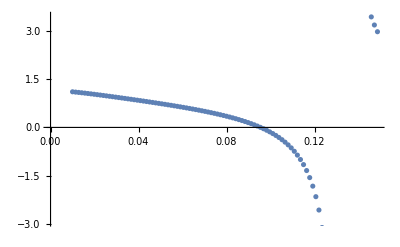

```mathematica
ListPlot[WROG[8]]
```

```mathematica
nomefile=StringJoin[{"Data/Control/Daeliminare.dat"}];
Save[nomefile,{WROG,(*WROD,*)minima}];
```

## Graphics

Importing file for the fundamental branch

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ReadList["Data/Control/FundBranch_stab_analysis.m"];
ReadList["Data/Control/SchwInstability.m"];
```

#### Unstable modes vs coupling value and vs Mass

```mathematica
UnstableOme=Table[{minima[[i,1]],-2minima[[i,3]]*minima[[i,2]]},{i,1,Length[minima]}];
GUnstableOme=Table[{Gminima[[i,1]],-2Gminima[[i,3]]*Gminima[[i,2]]},{i,1,Length[Gminima]}];
UnstableOmeMass=Table[{minima[[i,3]],2minima[[i,3]]*minima[[i,2]]},{i,1,Length[minima]}];
GUnstableOmeMass=Table[{Gminima[[i,3]],2Gminima[[i,3]]*Gminima[[i,2]]},{i,1,Length[Gminima]}];
SchUnstable=Table[{minimaSch[[i,1]],-minimaSch[[i,2]]},{i,5,Length[minimaSch]}];
```

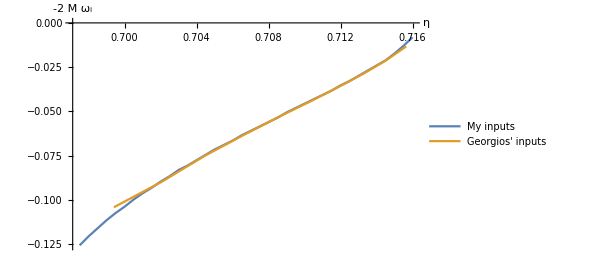

```mathematica
ListLinePlot[{Legended[UnstableOme[[1;;38]],"My inputs"],Legended[GUnstableOme,"Georgios' inputs"]},AxesLabel->{"η","-2 M ω_i"}]
```

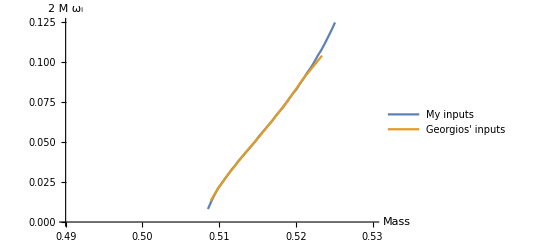

```mathematica
ListLinePlot[{Legended[UnstableOmeMass[[1;;38]],"My inputs"],Legended[GUnstableOmeMass,"Georgios' inputs"]},AxesLabel->{"Mass","2 M ω_i"},PlotRange->{{0.49,0.53},{0,0.125}}]
```

#### Schwarzschild unstable freq. vs fund. branch ones

My data for unstable modes of scalarized fundamental branch and for Schwarzschild solution. Second picture is just a magnification of the former.

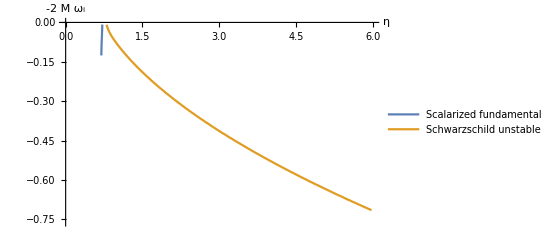

```mathematica
ListLinePlot[{Legended[UnstableOme[[1;;38]],"Scalarized fundamental branch"],Legended[SchUnstable,"Schwarzschild unstable modes"]},AxesLabel->{"η","-2 M ω_i"},PlotRange->{{0,6},{-0.76,0}}]
```

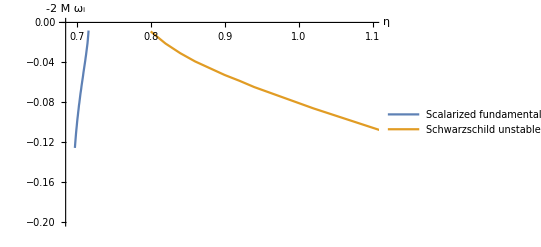

```mathematica
ListLinePlot[{Legended[UnstableOme[[1;;38]],"Scalarized fundamental branch"],Legended[SchUnstable,"Schwarzschild unstable modes"]},AxesLabel->{"η","-2 M ω_i"},PlotRange->{{0.685,1.1},{-0.2,0}}]
```

Georgios data that he already computed

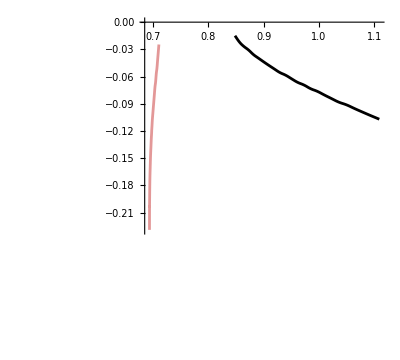

Georgios image that uses data that I do not have

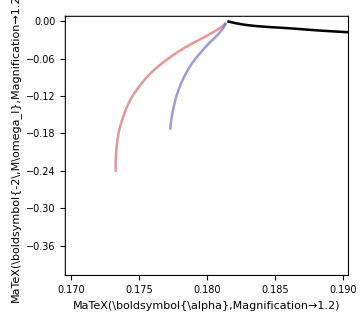

#### Wronskians vs ωi

```mathematica
tab=FundBranch;
maxnum=Length[tab]-3;
Table[Column[{Style[{tab[[num,1]],tab[[num,2]]},Darker@Blue,Bold,16],GraphicsRow[{ListPlot[WROD[num],PlotLabel->Style["Wrons_D",Blue]],ListPlot[WROG[num]//Abs,PlotLabel->Style["Wrons_G",Blue]](*,ListPlot[DPHIprod[num]]*)},ImageSize->{10^3,2*100}]},Alignment->Center],{num,1,maxnum}]
```

{}

#### New BOUNDARY CONDITIONS

```mathematica
ReadList["Data/Control/SchwInstability_newBCS.m"];
ReadList["Data/Control/FundBranch_GPINTEG_physicalBCK_newBCS.dat"];
```

```mathematica
SchUnstable2=Table[{minimaSch[[i,1]],-minimaSch[[i,2]]},{i,5,Length[minimaSch]}];
UnstableOmenew=Table[{(minima[[i,1]]/(2minima[[i,3]])^2),-2minima[[i,3]]*minima[[i,2]]},{i,1,Length[minima]}];
UnstableOmeMass2=Table[{minima[[i,3]]/Sqrt[minima[[i,1]]],2minima[[i,3]]*minima[[i,2]]},{i,1,Length[minima]}];
SchUnstableOmeMass2=Table[{0.5/Sqrt[minimaSch[[i,1]]],minimaSch[[i,2]]},{i,5,Length[minimaSch]}];
```

Difference between previous Schwarzschild solution and the new one

```mathematica
GraphicsRow[{ListLinePlot[{Legended[SchUnstable,"vecchie bcs"],Legended[SchUnstable2,"nuove bcs"]},ImageSize->{2.5*10^2,2*100}],ListLinePlot[{SchUnstable,SchUnstable2},PlotRange->{{0.7,1.2},{-0.15,0}}]}]
```

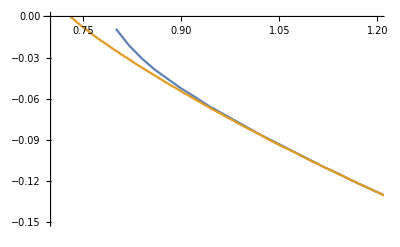

Plot of Schwarzschild unstable modes and fundamental branch

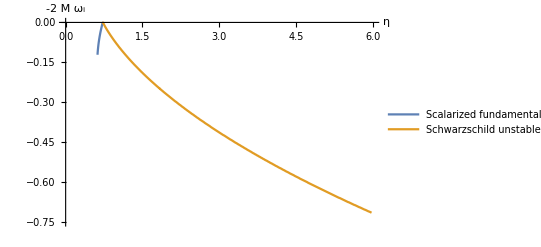

```mathematica
ListLinePlot[{Legended[UnstableOmenew,"Scalarized fundamental branch"],Legended[SchUnstable2,"Schwarzschild unstable modes"]},AxesLabel->{"η","-2 M ω_i"},PlotRange->{{0,6},{-0.75,0}}]
```

A magnification of the above plot

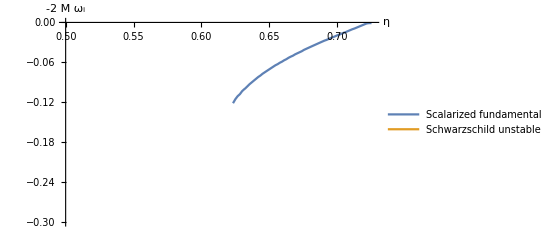

```mathematica
ListLinePlot[{Legended[UnstableOmenew,"Scalarized fundamental branch"],Legended[SchUnstable2,"Schwarzschild unstable modes"]},AxesLabel->{"η","-2 M ω_i"},PlotRange->{{0.5,0.726},{-0.3,0}}]
```

```mathematica
UnstableOmeMass2
```

{{0.628831,0.0992586},{0.628029,0.0960192},{0.62724,0.0927876},{0.626449,0.090085},{0.625671,0.0873889},{0.624889,0.0846968},{0.62412,0.0820109},{0.623346,0.0798508},{0.622583,0.0771743},{0.621815,0.0750227},{0.621056,0.0728756},{0.620295,0.0707318},{0.619539,0.0685922},{0.618784,0.0664562},{0.61803,0.0643238},{0.617281,0.0627138},{0.616527,0.060588},{0.615786,0.0589843},{0.615031,0.0568651},{0.614289,0.055267},{0.613542,0.0531551},{0.612797,0.0514387},{0.612059,0.0500039},{0.611311,0.0479426},{0.610573,0.0463896},{0.609833,0.0448389},{0.609091,0.0432907},{0.608356,0.0412428},{0.607616,0.0397004},{0.606876,0.0381604},{0.606143,0.0366234},{0.605408,0.0350889},{0.604668,0.0335567},{0.603933,0.0320274},{0.603203,0.0305008},{0.602469,0.0289766},{0.601732,0.0274548},{0.600997,0.0262423},{0.600265,0.0246957},{0.599535,0.0231518},{0.598805,0.0219147},{0.598075,0.0203758},{0.597344,0.0188395},{0.596613,0.0176093},{0.595883,0.016078},{0.595151,0.0148522},{0.594418,0.0133259},{0.593686,0.0118023},{0.592957,0.0102814},{0.592233,0.00906507},{0.591498,0.00754915},{0.590775,0.00603602},{0.590042,0.00452547},{0.589313,0.00301764},{0.588588,0.00152302},{0.587859,0.00100109},{0.587129,0.00100019}}

2Mωi vs the adimensional mass M/η^(1/2)

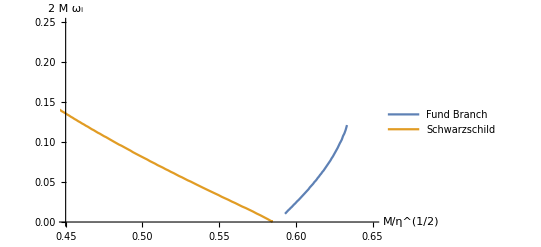

```mathematica
ListLinePlot[{Legended[UnstableOmeMass2[[1;;55]],"Fund Branch"],Legended[SchUnstableOmeMass2,"Schwarzschild"]},AxesLabel->{"   M/η^(1/2)","2 M ω_i"},PlotRange->{{0.45,0.65},{0,0.25}}]
```